```mathematica
(* Constructing 1d spin chain Hamiltonian *)
```

```mathematica
(*String join function for easy manipulation*)
S[xyz_,i_]:=ToExpression[StringJoin[{"S",ToString[xyz],ToString[i]}]];
comm[a_,b_]:=Return[a.b-b.a];
(*Tensor product of matrices*)
ToMatN[matlist_]:=Module[{n=Length[matlist],tensor=matlist⟦1⟧,i,j},
For[i=1,i<n,i++,tensor=Outer[Times,tensor,matlist⟦i+1⟧];];
For[j=1,j<n,j++,tensor=ArrayFlatten[tensor];];
Return[tensor];
]
```

```mathematica
makeoperator[type_,pos_,L_]:=Module[{tmp=Table[id,{i,1,L}]},tmp⟦pos+1⟧=slist⟦type+1⟧;Return[ToMatN[tmp]]]
```

```mathematica
sx=0.5{{0,1},{1,0}};
sy=0.5{{0,-I},{I,0}};
sz=0.5{{1,0},{0,-1}};
id={{1,0},{0,1}};
```

```mathematica
slist={sx,sy,sz,id};
```

```mathematica
OperatorToBuild[L_]:=Module[{oplist=Table[{0,0,0},{i,1,L}],posOp},
Do[oplist⟦hxi⟦1⟧+1,1⟧=1,{hxi,hx}];
Do[oplist⟦hyi⟦1⟧+1,2⟧=1,{hyi,hy}];
Do[oplist⟦hzi⟦1⟧+1,3⟧=1,{hzi,hz}];
Do[oplist⟦Jij⟦1⟧+1,1⟧=1;oplist⟦Jij⟦2⟧+1,1⟧=1,{Jij,Jxx}];
Do[oplist⟦Jij⟦1⟧+1,2⟧=1;oplist⟦Jij⟦2⟧+1,2⟧=1,{Jij,Jyy}];
Do[oplist⟦Jij⟦1⟧+1,3⟧=1;oplist⟦Jij⟦2⟧+1,3⟧=1,{Jij,Jzz}];
Return[oplist]
]
```

```mathematica
ConstructOperator[toconstruct_]:=Module[{todolist=Position[toconstruct,1]-1,pos,type},
operator=Table[{Null,Null,Null},{i,Range[L]}];
Do[
{pos,type}=p;
operator⟦pos+1,type+1⟧=makeoperator[type,pos,L];
,{p,todolist}
]
]
```

```mathematica
buildH[L_,dynamics_]:=Module[{staticH,dynamicH},
ConstructOperator[OperatorToBuild[L]];
staticH=Table[0,{i,1,2^L},{j,1,2^L}];
Do[staticH+=hxi[[2]]*operator⟦hxi[[1]]+1,1⟧,{hxi,hx}];
Do[staticH+=hyi[[2]]*operator⟦hyi[[1]]+1,2⟧,{hyi,hy}];
Do[staticH+=hzi[[2]]*operator⟦hzi[[1]]+1,3⟧,{hzi,hz}];
Do[staticH+=Jij[[3]]*operator⟦Jij[[1]]+1,1⟧.operator⟦Jij[[2]]+1,1⟧,{Jij,Jxx}];
Do[staticH+=Jij[[3]]*operator⟦Jij[[1]]+1,2⟧.operator⟦Jij[[2]]+1,2⟧,{Jij,Jyy}];
Do[staticH+=Jij[[3]]*operator⟦Jij[[1]]+1,3⟧.operator⟦Jij[[2]]+1,3⟧,{Jij,Jzz}];
dynamicH={};
Do[
(* Format of dynamics is {{positions1,type1,function1},...}, where function1[t] yields a number*)
AppendTo[dynamicH,{Total[operator⟦#+1,d[[2]]+1⟧&/@d[[1]]],d[[3]]}];,{d,dynamics}
];
Return[{staticH,dynamicH}]
];
```

```mathematica
L=2;
hx=Table[{i,0},{i,0,L-1}];
hy={};
hz=Table[{i,-0.2},{i,0,L-1}];
Jxx={};
Jyy={};
Jzz=Table[{i,Mod[i+1,L],1.0/0.809},{i,0,L-1}];
```

```mathematica
protocol={1.0,0.3,0.2,0.4,0.8};
```

```mathematica
function[t_]:=protocol[[t+1]]
```

```mathematica
system=buildH[2,{{{0,1},0,function}}]
```

{{{0.418047,0.,0.,0.},{0.,-0.618047,0.,0.},{0.,0.,-0.618047,0.},{0.,0.,0.,0.818047}},{{{{0.,0.5,0.5,0.},{0.5,0.,0.,0.5},{0.5,0.,0.,0.5},{0.,0.5,0.5,0.}},function}}}

```mathematica
evaluate[hfull_,t_]:=Module[{htot=hfull[[1]]},
Do[htot+=dyn[[2]][t]*dyn[[1]],{dyn,hfull[[2]]}];
Return[htot]
]
```

```mathematica
groundstate[h_]:=Sort[Thread[h//Eigensystem],#1[[1]]<#2[[1]]&][[1]]
```

```mathematica
evaluate[system,0]
```

{{0.418047,-0.25,-0.25,0.},{-0.25,-0.618047,0.,-0.25},{-0.25,0.,-0.618047,-0.25},{0.,-0.25,-0.25,0.818047}}

```mathematica
psi={-0.38481418435664777,-0.6152929510290139,-0.6152929510290137,-0.307810351265098};
```

```mathematica
Module[{tmp,t,state},
state=psi;
For[t=0,t<5,t++,
state=MatrixExp[-I*0.05*evaluate[system,t],state]
];
state
]
```

```mathematica
evaluate[system,0]//groundstate
```

{-1.18089,{0.384814,-0.615293,-0.615293,0.30781}}

```mathematica
target={0.38481418435664777,-0.6152929510290139,-0.6152929510290137,0.307810351265098};
```

```mathematica
evol=-{-0.38730316885578764+0.0767176000181895 ⅈ,-0.604095719375971-0.07377263745517382 ⅈ,-0.6040957193759708-0.0737726374551738 ⅈ,-0.30579482563557253+0.09925779286935717 ⅈ};
```

```mathematica
Norm[evol.target]^2
```

0.272983

```mathematica
3^40
```

12157665459056928801

```mathematica
(1/0.01-1)/100.
```

0.99

```mathematica
MovingAverage[{0.2,0.3,0.4,0.5,0.6,0.9},3]
```

{0.3,0.4,0.5,0.666667}

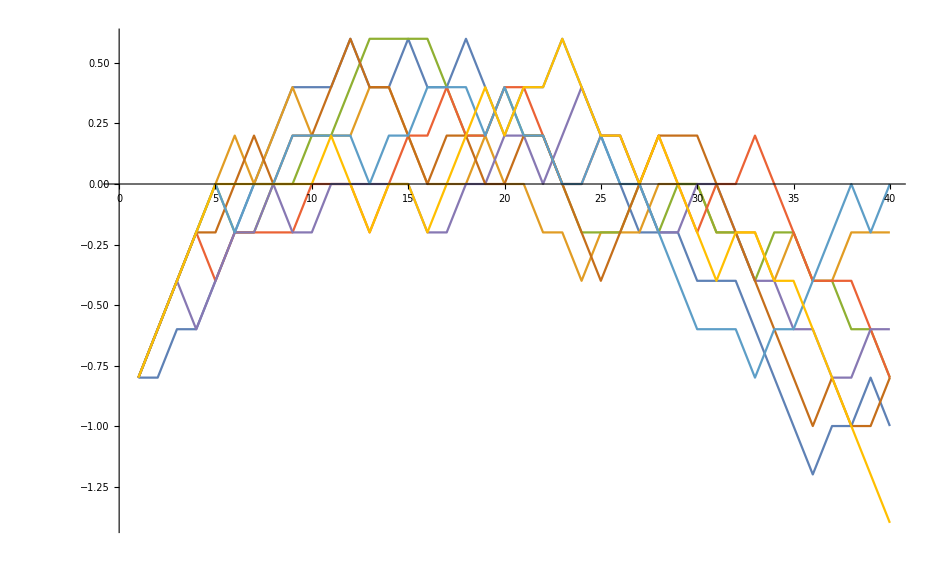

```mathematica
h={{-0.8,-0.8,-0.6,-0.6,-0.4,-0.2,0.,0.2,0.4,0.4,0.4,0.6,0.4,0.4,0.6,0.4,0.4,0.6,0.4,0.2,0.4,0.4,0.6,0.4,0.2,0.,-0.2,-0.2,-0.2,-0.4,-0.4,-0.4,-0.6,-0.8,-1.,-1.2,-1.,-1.,-0.8,-1.},
{-0.8,-0.6,-0.4,-0.2,0.,0.2,0.,0.2,0.4,0.2,0.2,0.2,0.4,0.4,0.2,0.,0.,0.,0.2,0.,0.,-0.2,-0.2,-0.4,-0.2,-0.2,-0.2,0.,0.,0.,-0.2,-0.2,-0.2,-0.4,-0.2,-0.4,-0.4,-0.2,-0.2,-0.2},
{-0.8,-0.6,-0.4,-0.2,0.,-0.2,-0.2,0.,0.,0.2,0.2,0.4,0.6,0.6,0.6,0.6,0.4,0.2,0.2,0.4,0.2,0.2,0.,-0.2,-0.2,-0.2,0.,-0.2,0.,0.,-0.2,-0.2,-0.4,-0.2,-0.2,-0.4,-0.4,-0.6,-0.6,-0.8},
{-0.8,-0.6,-0.4,-0.2,-0.4,-0.2,-0.2,-0.2,-0.2,0.,0.,0.,-0.2,0.,0.2,0.2,0.4,0.2,0.2,0.4,0.4,0.2,0.,0.,0.2,0.2,0.,0.2,0.,-0.2,0.,0.,0.2,0.,-0.2,-0.4,-0.4,-0.4,-0.6,-0.8},{-0.8,-0.6,-0.4,-0.6,-0.4,-0.2,-0.2,0.,-0.2,-0.2,0.,0.,0.,0.,0.,-0.2,-0.2,0.,0.,0.2,0.2,0.,0.2,0.4,0.2,0.2,0.,-0.2,-0.2,0.,0.,-0.2,-0.4,-0.4,-0.6,-0.6,-0.8,-0.8,-0.6,-0.6},
{-0.8,-0.6,-0.4,-0.2,-0.2,0.,0.2,0.,0.2,0.2,0.4,0.6,0.4,0.4,0.2,0.,0.2,0.2,0.,0.,0.2,0.2,0.,-0.2,-0.4,-0.2,0.,0.2,0.2,0.2,0.,-0.2,-0.4,-0.6,-0.8,-1.,-0.8,-1.,-1.,-0.8},
{-0.8,-0.6,-0.4,-0.2,0.,-0.2,0.,0.,0.2,0.2,0.2,0.2,0.,0.2,0.2,0.4,0.4,0.4,0.2,0.4,0.2,0.2,0.,0.,0.2,0.,0.,-0.2,-0.4,-0.6,-0.6,-0.6,-0.8,-0.6,-0.6,-0.4,-0.2,0.,-0.2,0.},
{-0.8,-0.6,-0.4,-0.2,0.,0.,0.,0.,0.,0.,0.2,0.,-0.2,0.,0.,-0.2,0.,0.2,0.4,0.2,0.4,0.4,0.6,0.4,0.2,0.2,0.,0.2,0.,-0.2,-0.4,-0.2,-0.2,-0.4,-0.4,-0.6,-0.8,-1.,-1.2,-1.4}
};
ListLinePlot[h]
```

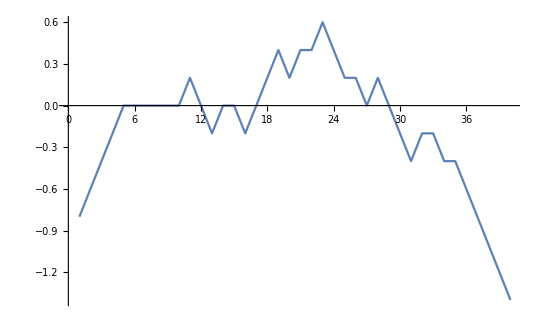

```mathematica
ListLinePlot[h[[-1]]]
```

```mathematica
2^10
```

1024

```mathematica
[-1.-0.6-0.8-0.8-0.8-0.72-0.64-1.44-1.46-1.46-1.56-1.16-1.18-1.18-1.28-1.28-1.36-1.36-1.36-1.38-1.38-1.46-1.56-0.76-0.66-0.56-0.16-0.16-0.16-0.16-0.16-0.18 0.22 0.22 0.32 0.32 0.32 0.32 0.32 0.32-0.08]
```

```mathematica
3.5/40.
```

0.0875

```mathematica
Log[2.,40^10]
```

53.2193

```mathematica
hp=RandomSample[{-0.2,0,0.2},20]
```

RandomSample[{-0.2,0,0.2},20]

```mathematica
Table[RandomSample[{-0.2,0,0.2},1],{i,1,40}]//Flatten
```

{0.2,-0.2,0.2,-0.2,-0.2,0,0.2,-0.2,0,-0.2,0.2,0.2,-0.2,0,0,-0.2,0.2,-0.2,-0.2,0.2,0,0.2,-0.2,0.2,0.2,0,-0.2,-0.2,0,-0.2,0.2,0,0,0,0,-0.2,0,0.2,-0.2,0.2}

```mathematica
Accumulate[Table[RandomSample[{-0.2,0,0.2},1],{i,1,40}]//Flatten]
```

{-0.2,0.,0.2,0.2,0.2,0.4,0.4,0.2,0.4,0.2,0.2,0.4,0.6,0.4,0.4,0.6,0.8,0.6,0.6,0.6,0.4,0.6,0.4,0.2,0.2,0.2,0.2,5.55112×10^-17,0.2,5.55112×10^-17,0.2,0.4,0.6,0.8,1.,1.,0.8,1.,1.,1.2}

```mathematica
hp=Accumulate[Table[RandomSample[{-0.2,0,0.2},1],{i,1,40}]//Flatten]
```

{0,0.2,0.4,0.2,0.,0.2,0.,-0.2,-0.2,-0.2,-0.4,-0.6,-0.8,-1.,-0.8,-1.,-1.,-1.,-0.8,-0.8,-1.,-1.2,-1.2,-1.4,-1.6,-1.8,-2.,-1.8,-1.6,-1.6,-1.8,-1.6,-1.8,-2.,-1.8,-2.,-1.8,-1.6,-1.8,-1.6}

```mathematica
hp[[1]]
```

0

```mathematica
Clear[H]
H[t_]:={{-0.5,0},{0,0.5}}+hp[[t]]{{0,1},{1,0}}
```

```mathematica
Product@@Table[MatrixExp[H[t]],{t,1,40}]
```

Product[{{0.606531,0.},{0.,1.64872}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.677227,0.427899},{0.427899,1.74697}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.606531,0.},{0.,1.64872}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.606531,0.},{0.,1.64872}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.677227,-0.427899},{-0.427899,1.74697}},{{0.768416,-0.662888},{-0.662888,1.87323}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.082,-1.22175},{-1.22175,2.30375}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.31769,-1.56774},{-1.56774,2.62414}},{{1.31769,-1.56774},{-1.56774,2.62414}},{{1.61848,-1.97574},{-1.97574,3.02972}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}}]

```mathematica
Table[MatrixExp[H[t]],{t,1,40}]
```

{{{0.606531,0.},{0.,1.64872}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.677227,0.427899},{0.427899,1.74697}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.606531,0.},{0.,1.64872}},{{0.624019,0.209808},{0.209808,1.67306}},{{0.606531,0.},{0.,1.64872}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.624019,-0.209808},{-0.209808,1.67306}},{{0.677227,-0.427899},{-0.427899,1.74697}},{{0.768416,-0.662888},{-0.662888,1.87323}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.082,-1.22175},{-1.22175,2.30375}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{0.901461,-0.924061},{-0.924061,2.05654}},{{1.082,-1.22175},{-1.22175,2.30375}},{{1.31769,-1.56774},{-1.56774,2.62414}},{{1.31769,-1.56774},{-1.56774,2.62414}},{{1.61848,-1.97574},{-1.97574,3.02972}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{3.0552,-3.75004},{-3.75004,4.93022}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}},{{2.46936,-3.04564},{-3.04564,4.16138}},{{1.99706,-2.46194},{-2.46194,3.53577}}}

```mathematica
Dot@@@Table[MatrixExp[H[t]],{t,1,40}]
```

{0.,0.481945,1.03731,0.481945,0.,0.481945,0.,-0.481945,-0.481945,-0.481945,-1.03731,-1.75111,-2.73337,-4.13654,-2.73337,-4.13654,-4.13654,-4.13654,-2.73337,-2.73337,-4.13654,-6.17975,-6.17975,-9.18364,-13.6215,-20.1949,-29.9456,-20.1949,-13.6215,-13.6215,-20.1949,-13.6215,-20.1949,-29.9456,-20.1949,-29.9456,-20.1949,-13.6215,-20.1949,-13.6215}

```mathematica
Apply[Dot,Dot@@@Table[MatrixExp[H[t]],{t,1,40}]]
```

0..0.481945.1.03731.0.481945.0..0.481945.0..(-0.481945).(-0.481945).(-0.481945).(-1.03731).(-1.75111).(-2.73337).(-4.13654).(-2.73337).(-4.13654).(-4.13654).(-4.13654).(-2.73337).(-2.73337).(-4.13654).(-6.17975).(-6.17975).(-9.18364).(-13.6215).(-20.1949).(-29.9456).(-20.1949).(-13.6215).(-13.6215).(-20.1949).(-13.6215).(-20.1949).(-29.9456).(-20.1949).(-29.9456).(-20.1949).(-13.6215).(-20.1949).(-13.6215)

```mathematica
ParallelCombine[Dot[Sequence@@##]&,Table[MatrixExp[H[t]],{t,1,40}],Dot]
```

$Aborted

```mathematica
ParallelCombine[Dot[Sequence@@##]&,Table[MatrixExp[H[t]],{t,1,40}],Dot]
```

{{-1.4245×10^20,1.93537×10^20},{-1.72123×10^21,2.33852×10^21}}

```mathematica
Table[MatrixExp[H[t]],{t,1,40}]
```

Product[Table[MatrixExp[H[t]],{t,1,40}]]

```mathematica
{{0.1-0.1},{-0.1-0.1}}
```

{{0.},{-0.2}}

```mathematica
MatrixExp[-I*0.05*{{0.1,-0.1},{-0.1,-0.1}},{0,-1}]//MatrixForm
```

(-2.63522×10^-21-0.00499996 ⅈ
-0.999975-0.00499996 ⅈ)